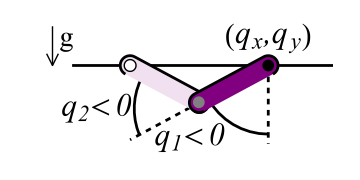
-Graphics-

Based on the model above [1] with continuation results from [2].  The code presented here is mainly to test the NLink code against a known system.  A simpler tutorial version of how to use NLink can be found in GoswamiEtAl.nb.

[1] Rosa,N., A.Barber, R.D.Gregg, and K.M.Lynch, "Stable open-loop brachiation on a vertical wall", Robotics and Automation (ICRA),2012.
 
[2] Rosa, N., and K. M. Lynch, “The Passive Dynamics of Walking and Brachiating Robots: Results on the Topology and Stability of Passive Gaits”, International Conference on Climbing and Walking Robots, 2013.

## Recursive Newton-Euler + Composite Rigid Body Algorithm

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../"];
SetOptions[NDSolve, AccuracyGoal-> 13, PrecisionGoal-> 13, 
Compiled-> False, MaxSteps-> Infinity];
<<"NLink`";
SetDirectory[NotebookDirectory[]];
```

```mathematica
n = 2; (* # of bodies *)

(* physical parameters in SI units used in [1] *)
(* we'll place them in a function for now, so we can run tests symbolically *)
PhysicalParameters[] := Module[{},
(* mass and inertia *)
m1=3.083276839957533; (* link mass *)
m2=3.083276839957533;
I1=5.386568898408416*^-2; (* inertia about c.o.m *)I2=5.386568898408416*^-2;

(* lengths *)
L1=0.610; (* link length *)
L2=0.610;
r2=6.37687066165708*^-2; (* distance to c.o.m *)
r1=L1-r2;

(* gravity *)
g=9.81;

(* scaling factors *)
d = L1 + L2; (* length *)
dt = Sqrt[d/g];
du = g m2 r2;
]
```

```mathematica
frames = ConstantArray[0, {n, 6}];
(* frames is a list of spatial vectors {rx, ry, rz, px, py, pz} defining the location of frame i in frame (i-1) coordinates when the robot is at its "home" configuration. *)
frames⟦2, 5⟧ = -L1/d;

frames // N // MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -(1. L1)/d | 0.)

```mathematica
inertia = ConstantArray[0, {n, 10}];
(* inertia is a list of mass parameters about the center of mass and their location {m, rx, ry, rz, px, py, pz, Ixx, Iyy, Izz} of link i in link i coordinates; cross inertia terms, e.g., Ixy, are also supported. *)

inertia⟦1, {1, 6, 10}⟧ = {d m1/(m2 r2) , -r1/d, I1/ (d m2 r2)};
inertia⟦2, {1, 6, 10}⟧ =  {d m2/(m2 r2), -r2/d, I2/ (d m2 r2)};

inertia // N// MatrixForm
```

((d m1)/(m2 r2) | 0. | 0. | 0. | 0. | -(1. r1)/d | 0. | 0. | 0. | I1/(d m2 r2)
d/r2 | 0. | 0. | 0. | 0. | -(1. r2)/d | 0. | 0. | 0. | I2/(d m2 r2))

```mathematica
(* robot description *)
parent = Range[2]-1; (* kinematic chain *)
joints = {"pln", "rz"};
nd = 2Length@NLink`Private`ExpandJoints[joints] + 4;
b = {{1,0}, {1,0}};
r = {{{0,0,0,1,0,0}, {0,0,0,1,0,0}}, {{0,0,0,0,1,0}, {0,0,0,0,1,0}}};
SetModel[joints, parent, {b,r}, {0, g dt^2/d, 0}, inertia, frames, nd];
```